```mathematica
eps=0.1;
```

```mathematica
rx=5;
```

### Make a density function

```mathematica
density[x_,y_,z_]:=1/(Norm[{x,y,z}-{-1,0,0}]+eps)+1/(Norm[{x,y,z}-{1,0,0}]+eps)
```

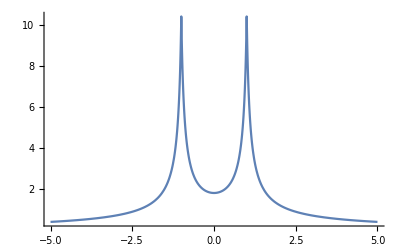

```mathematica
Plot[density[x,0,0],{x,-5,5},PlotRange->All]
```

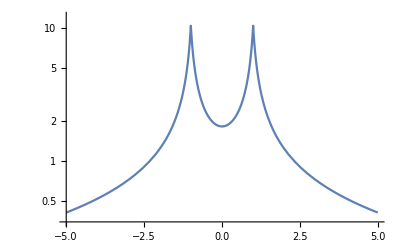

```mathematica
LogPlot[density[x,0,0],{x,-5,5},PlotRange->All]
```

### A 2 D plot of Log10 density

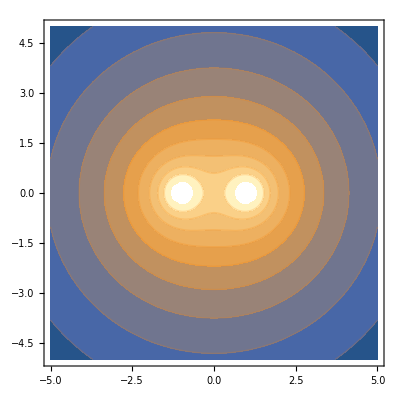

```mathematica
ContourPlot[Log10[density[x,y,0]],{x,-rx,rx},{y,-rx,rx},Contours->Automatic,ContourStyle->Directive[Orange,Opacity[0.2],Specularity[White,30]],Mesh->None]
```

### A 3D plot

```mathematica
DensityPlot3D[Log10[density[x,y,z]],{x,-rx,rx},{y,-rx,rx},{z,-rx,rx},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

### 3D in a ball region that intersects the sources

```mathematica
DensityPlot3D[Log10[density[x,y,z]],{x,y,z}∈Ball[{0,0,0},1],AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

### 3D in a rectangular region that creates a slice

```mathematica
DensityPlot3D[Log10[density[x,y,z]],{x,y,z}∈ImplicitRegion[-rx≤x≤rx&&-rx≤z≤rx&&0≤y≤rx,{x,y,z}],AxesLabel->{"X","Y","Z"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-